# Bruker 1D Data Import and SpinDynamica Signal Workflow

## Importing processed TopSpin 1D NMR spectra (1r/1i, procs/acqus), intensity scaling, chemical-shift calibration, visualization, inverse-FFT Signal conversion, and interactive binary synthesis labs.

## 0. Setup and Loading SpinDynamica

Evaluate the two setup cells below. Cell 1 locates the repository checkout root upward from NotebookDirectory[] and loads SpinDynamica` before referencing any package symbol. Cell 2 verifies that Signals`Bruker` loaded cleanly.

```mathematica
nbRepoRoot = Module[{dir = Quiet[Check[NotebookDirectory[], Directory[]]], found = None},
  Do[
    If[FileExistsQ[FileNameJoin[{dir, "SpinDynamica", "SpinDynamica.m"}]],
      found = dir; Break[]];
    dir = ParentDirectory[dir],
    {6}
  ];
  If[found === None && FileExistsQ[FileNameJoin[{Directory[], "SpinDynamica", "SpinDynamica.m"}]],
    found = Directory[]];
  found
];
If[StringQ[nbRepoRoot],
  Needs["SpinDynamica`", FileNameJoin[{nbRepoRoot, "SpinDynamica", "SpinDynamica.m"}]],
  Needs["SpinDynamica`"]
];
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

```mathematica
SetUserLevel[2];
<|
  "SpinDynamicaFile" -> FindFile["SpinDynamica`"],
  "Version" -> $SpinDynamicaVersion,
  "SignalsBrukerSymbols" -> Length[Names["Signals`Bruker`*"]],
  "SampleDataExists" -> DirectoryQ[FileNameJoin[{nbRepoRoot, "sample_data"}]]
|>
```

SetUserLevel::nochge: The user level is already set to 2. No action has been taken.

<|SpinDynamicaFile→C:\Users\cb1d19\AppData\Roaming\Wolfram\Paclets\Repository\SpinDynamica-3.14.3\SpinDynamica\SpinDynamica.m,Version→SDv3.10.3b3 (modified by Google Anti-Gravity Neon),SignalsBrukerSymbols→15,SampleDataExists→True|>

## Introduction

The Signals`Bruker` package (SpinDynamica/Signals/Bruker.m) brings experimental Bruker TopSpin 1D processed spectra directly into SpinDynamica without external conversion tools or hidden normalization.

Import from an experiment root, a pdata directory, a specific pdata/<n> directory, or a direct 1r file path.

Preserve Bruker 2^NC_proc physical scaling (IntensityScaling -> "Bruker") alongside packed RawReal / RawImaginary arrays.

Plot spectra on SpinDynamica/NMR conventions via PlotBrukerSpectrum or ListPlot, apply zero-order phase rotations, and convert spectra back into time-domain Signal objects via ToSignal.

## Mathematical Background

Authoritative TopSpin processing status parameters are read strictly from procs (not queued proc): DTYPP selects 32-bit signed integers (0) or 64-bit IEEE floats (2), BYTORDP selects little-endian (0) or big-endian (1), and Npts equals STSI if STSI > 0 else SI. Stored integers or floats y_raw[k] map to physical intensity y_phys[k] = y_raw[k] * 2^NC_proc. With OFFSET giving the first-point chemical shift, SW_p the processed spectral width in Hz, and SF the spectrometer reference frequency in MHz, point k has chemical shift delta_k = OFFSET - (k/(Npts - 1)) * (SW_p / SF), frequency nu_k = delta_k * SF, and angular frequency omega_k = 2 Pi nu_k (reversed when REVERSE = yes).

## Worked Example

Load sample_data, compare scaling modes, inspect acquisition and processing metadata, locate the dominant resonance peak, plot both ppm and zoomed Hz views, apply a phase rotation, and verify a ToSignal -> FT round-trip to < 1e-13 relative error.

```mathematica
sampleDir = FileNameJoin[{nbRepoRoot, "sample_data"}];
spec = ImportBrukerSpectrum[sampleDir];
specRaw = ImportBrukerSpectrum[sampleDir, IntensityScaling -> "Raw"];
specNorm = ImportBrukerSpectrum[sampleDir, IntensityScaling -> "Normalized"];

peakIdx = First[Ordering[spec["Real"], -1]];
peakPPM = spec["ChemicalShift"][[peakIdx]];
peakHz = spec["Frequency"][[peakIdx]];

procs = spec["ProcessingParameters"];
acqus = spec["AcquisitionParameters"];

<|
  "Object" -> ToString[spec, OutputForm],
  "Title" -> spec["Title"],
  "Nucleus" -> spec["Nucleus"],
  "SF_MHz" -> spec["ReferenceFrequencyMHz"],
  "SW_Hz" -> spec["SpectralWidthHz"],
  "NumPoints" -> spec["NumPoints"],
  "NC_proc" -> spec["NCProc"],
  "MaxRaw" -> Max[specRaw["RawReal"]],
  "MaxBrukerScaled" -> Max[spec["Real"]],
  "MaxNormalizedMag" -> Max[Abs[specNorm["Complex"]]],
  "PeakPPM" -> peakPPM,
  "PeakHz" -> peakHz,
  "AcqusSummary" -> <|"PULPROG" -> acqus["PULPROG"], "TD" -> acqus["TD"], "NS" -> acqus["NS"], "MASR_Hz" -> acqus["MASR"]|>,
  "ProcsSummary" -> <|"LB" -> procs["LB"], "PHC0" -> procs["PHC0"], "F1P" -> procs["F1P"], "F2P" -> procs["F2P"]|>
|>
```

<|Object→BrukerSpectrum[1H, 131072 pts, SF=299.83 MHz, 8.338..-8.338 ppm, complex],Title→0.4 V COil p1=120
PC Thermal bond chip 48 symmetric channels (175+500+175)
Condition 1: bruker label face you and coil connector facing away label - for whole experiment
A6,Nucleus→1H,SF_MHz→299.833,SW_Hz→5000.,NumPoints→131072,NC_proc→-10,MaxRaw→387887124,MaxBrukerScaled→378796.,MaxNormalizedMag→1.,PeakPPM→-1.99335,PeakHz→-597.672,AcqusSummary→<|PULPROG→gp_echozg,TD→65536,NS→1,MASR_Hz→4200|>,ProcsSummary→<|LB→1,PHC0→113.2,F1P→8.33798,F2P→-8.33798|>|>

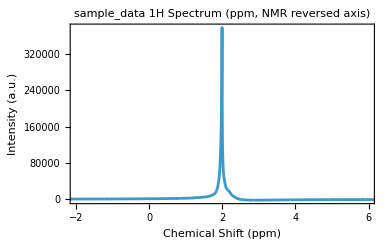
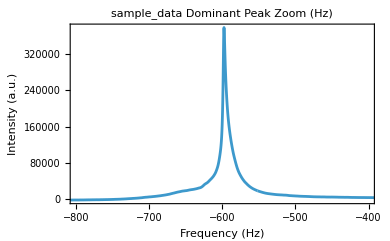
-Graphics--Graphics-
Phased peak max=384416. | ToSignal -> FT relative error = 3.33×10^-16

```mathematica
pltPPM = PlotBrukerSpectrum[spec, PlotRange -> {{-6, 2}, All},
  PlotLabel -> "sample_data 1H Spectrum (ppm, NMR reversed axis)"];
pltHz = PlotBrukerSpectrum[spec, AxisUnits -> "Hz", Component -> "Real",
  PlotRange -> {{-800, -400}, All}, PlotLabel -> "sample_data Dominant Peak Zoom (Hz)"];

specPhased = Exp[I * (30. * Degree)] * spec;
sigTD = ToSignal[spec];
ftCheck = FT[sigTD, ZeroFill -> 1, FirstPointMultiplicationFactor -> 1];
rtErr = Max[Abs[Reverse[ftCheck[[All, 2]]] - spec["Complex"]]] / Max[Abs[spec["Complex"]]];

Column[{
  Row[{Show[pltPPM, ImageSize -> 390], Spacer[12], Show[pltHz, ImageSize -> 390]}],
  Style[StringForm["Phased peak max=`1` | ToSignal -> FT relative error = `2`",
    NumberForm[Max[specPhased["Real"]], 6], ScientificForm[rtErr, 3]], "Text"]
}]
```

## Interactive Exploration

Lab S1A lets you inspect sample_data instantaneously across AxisUnits, Component, zero-order phase rotation, and zoom half-width. Lab S1B (queued button) writes an isolated synthetic Bruker dataset with configurable binary encoding (DTYPP/BYTORDP/NC_proc/STSI/REVERSE), re-imports it with ImportBrukerSpectrum, and verifies exact numerical reconstruction.

```mathematica
renderLabS1A[specObj_BrukerSpectrum, unit_String, comp_String, phc0Deg_?NumericQ, halfSpan_] := Module[
  {phSpec, pIdx, centerVal, rng, lbl},
  phSpec = If[Abs[phc0Deg] < 1.*^-12, specObj, Exp[I * (phc0Deg * Degree)] * specObj];
  pIdx = First[Ordering[Abs[specObj["Complex"]], -1]];
  centerVal = Switch[unit,
    "ppm", specObj["ChemicalShift"][[pIdx]],
    "Hz", specObj["Frequency"][[pIdx]],
    _, specObj["AngularFrequency"][[pIdx]]
  ];
  rng = If[halfSpan === All, All,
    With[{sc = Switch[unit, "ppm", 1., "Hz", specObj["ReferenceFrequencyMHz"], _, 2. Pi * specObj["ReferenceFrequencyMHz"]]},
      {Sort[{centerVal - halfSpan * sc, centerVal + halfSpan * sc}], All}
    ]
  ];
  lbl = StringForm["sample_data (`1`, `2`, phc0=`3` deg)", unit, comp, NumberForm[phc0Deg, {4, 1}]];
  PlotBrukerSpectrum[phSpec, AxisUnits -> unit, Component -> comp, PlotRange -> rng, PlotLabel -> lbl, ImageSize -> 580]
];

runLabS1B[dtypp_Integer, bytordp_Integer, ncProc_Integer, stripLen_Integer, revQ_] := Module[
  {tmpDir, pdir, nSI = 64, ppm0, delta, lor, rAll, iAll, nUse, bo, fmt, pLines, st,
   imported, expectR, expectI, scaleF, errR, errI, plt},
  tmpDir = FileNameJoin[{$TemporaryDirectory, "sd_nb_bruker_" <> ToString[$ProcessID] <> "_" <> ToString[RandomInteger[{10000, 99999}]]}];
  pdir = FileNameJoin[{tmpDir, "pdata", "1"}];
  CreateDirectory[pdir, CreateIntermediateDirectories -> True];
  ppm0 = Subdivide[8.0, 0.0, nSI - 1];
  delta = ppm0 - 3.2;
  lor = 1. / (1. + (delta / 0.28)^2) + I * (- (delta / 0.28) / (1. + (delta / 0.28)^2));
  rAll = If[dtypp === 0, Round[40000. * Re[lor]], N[400. * Re[lor]]];
  iAll = If[dtypp === 0, Round[40000. * Im[lor]], N[400. * Im[lor]]];
  nUse = Min[Max[16, stripLen], nSI];
  rAll = rAll[[1 ;; nUse]]; iAll = iAll[[1 ;; nUse]];

  bo = If[bytordp === 0, -1, 1];
  fmt = If[dtypp === 0, "Integer32", "Real64"];
  pLines = {
    "##TITLE= Synthetic Notebook Bruker Fixture",
    "##JCAMPDX= 5.0",
    "##$SI= " <> ToString[nSI],
    If[nUse < nSI, "##$STSI= " <> ToString[nUse], Nothing],
    If[nUse < nSI, "##$STSR= 1", Nothing],
    "##$SF= 400.0",
    "##$SW_p= 3200.0",
    "##$OFFSET= 8.0",
    "##$BYTORDP= " <> ToString[bytordp],
    "##$DTYPP= " <> ToString[dtypp],
    "##$NC_proc= " <> ToString[ncProc],
    "##$REVERSE= " <> If[TrueQ[revQ], "yes", "no"],
    "##$AXNUC= <1H>",
    "##END="
  } /. Nothing -> Sequence[];
  Export[FileNameJoin[{pdir, "procs"}], pLines, "Lines"];
  st = OpenWrite[FileNameJoin[{pdir, "1r"}], BinaryFormat -> True];
  BinaryWrite[st, rAll, fmt, ByteOrdering -> bo]; Close[st];
  st = OpenWrite[FileNameJoin[{pdir, "1i"}], BinaryFormat -> True];
  BinaryWrite[st, iAll, fmt, ByteOrdering -> bo]; Close[st];

  imported = ImportBrukerSpectrum[tmpDir];
  Quiet[DeleteDirectory[tmpDir, DeleteContents -> True]];
  scaleF = N[2.^ncProc];
  expectR = N[rAll] * scaleF;
  expectI = N[iAll] * scaleF;
  errR = Max[Abs[imported["Real"] - expectR]];
  errI = Max[Abs[imported["Imaginary"] - expectI]];
  plt = PlotBrukerSpectrum[imported, Component -> "Both",
    PlotLabel -> StringForm["Synthetic 1D (`1`, `2`, NC_proc=`3`, pts=`4`)",
      imported["DataType"], imported["ByteOrder"], ncProc, nUse],
    ImageSize -> 540];
  <|
    "DataType" -> imported["DataType"],
    "ByteOrder" -> imported["ByteOrder"],
    "NumPoints" -> imported["NumPoints"],
    "NCProc" -> imported["NCProc"],
    "ScaleFactor" -> imported["AppliedScaleFactor"],
    "FirstPPM" -> First[imported["ChemicalShift"]],
    "LastPPM" -> Last[imported["ChemicalShift"]],
    "MaxRealError" -> errR,
    "MaxImagError" -> errI,
    "Plot" -> plt
  |>
];

renderLabS1B[d_Association] := Column[{
  Grid[{
    {"DataType / ByteOrder:", d["DataType"] <> " / " <> d["ByteOrder"], "Points:", d["NumPoints"]},
    {"NC_proc / Scale:", Row[{d["NCProc"], " (", NumberForm[d["ScaleFactor"], 4], ")"}], "PPM Range:", Row[{NumberForm[d["FirstPPM"], 4], " .. ", NumberForm[d["LastPPM"], 4]}]},
    {"Max Real Error:", ScientificForm[d["MaxRealError"], 3], "Max Imag Error:", ScientificForm[d["MaxImagError"], 3]}
  }, Frame -> All, Alignment -> Left],
  d["Plot"]
}];

labS1BDefault = runLabS1B[0, 0, -4, 64, False];
{labS1BDefault["MaxRealError"], labS1BDefault["MaxImagError"]}
```

{0.,0.}

```mathematica
Manipulate[
  renderLabS1A[spec, axisU, compS, phDeg, zoomW],
  {{axisU, "ppm", "Axis Units"}, {"ppm", "Hz", "rad/s"}},
  {{compS, "Real", "Component"}, {"Real", "Imaginary", "Both", "Magnitude"}},
  {{phDeg, 0., "Zero-Order Phase (deg)"}, -180., 180., 5., Appearance -> "Labeled"},
  {{zoomW, 3., "Half-Span (ppm equiv)"}, {0.5 -> "0.5 ppm", 3. -> "3 ppm", 8. -> "8 ppm", All -> "Full SW"}}
]
```

```mathematica
DynamicModule[{dt = 0, bo = 0, nc = -4, stsi = 64, rev = False, res = labS1BDefault},
  Panel[Column[{
    Grid[{
      {"Binary DTYPP:", SetterBar[Dynamic[dt], {0 -> "Integer32 (0)", 2 -> "Real64 (2)"}]},
      {"Byte Ordering:", SetterBar[Dynamic[bo], {0 -> "Little-Endian (0)", 1 -> "Big-Endian (1)"}]},
      {"Scale NC_proc:", Row[{Slider[Dynamic[nc], {-6, 4, 1}], " ", Dynamic[nc]}]},
      {"Strip STSI:", SetterBar[Dynamic[stsi], {32 -> "32 (strip)", 64 -> "64 (full SI)"}]},
      {"REVERSE Axis:", Checkbox[Dynamic[rev]]}
    }, Alignment -> Left],
    Button["Build & Import Synthetic Dataset",
      res = runLabS1B[dt, bo, nc, stsi, rev],
      Method -> "Queued"],
    Dynamic[renderLabS1B[res]]
  }]]
]
```

## Suggested Experiments

1. Phase alignment: Drag Zero-Order Phase (deg) in Lab S1A away from 0 deg and observe dispersive mixing, then switch Component to "Magnitude" to verify phase invariance.

2. Physical frequency check: Switch Axis Units between "ppm" (descending NMR convention) and "Hz" / "rad/s" (ascending) and confirm the dominant resonance at -1.99 ppm corresponds to -597.7 Hz at SF = 299.83 MHz.

3. Binary portability: In Lab S1B, switch DTYPP = 2 (Real64) and Byte Ordering = 1 (Big-Endian) and confirm Max Real/Imag Error stays near machine precision (~0 to 1e-13).

4. Strip transform & REVERSE: Compare STSI = 32 against 64 and toggle REVERSE to verify exact axis truncation and direction reversal.

## Summary

Signals`Bruker` cleanly bridges TopSpin experimental 1D data and SpinDynamica simulation/signal workflows with exact binary fidelity, physical units, packed-array efficiency, and lossless ToSignal -> FT round-trips.

See also 00_GeneralOptimization_Tutorials_Index.nb or run Examples/Signals/Tutorial_Bruker1DImport.wls and documentation/Signals/Bruker_Data_Import_Guide.md.